### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,1}};
Data["Exit Vertices and Terminal Costs"]={{10,1000}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.023997,Null}

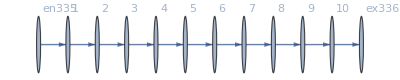

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j337→1.,j338→1.,j339→1.,j340→1.,j341→1.,j342→1.,j343→1.,j344→1.,j345→1.,j346→1.,j347→1.,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1.,jt361→1.,jt362→0.,jt363→1.,jt364→0.,jt365→1.,jt366→0.,jt367→1.,jt368→0.,jt369→1.,jt370→0.,jt371→1.,jt372→0.,jt373→1.,jt374→0.,jt375→1.,jt376→0.,jt377→1.,jt378→0.,u379→1009.,u380→1008.,u381→1007.,u382→1006.,u383→1005.,u384→1004.,u385→1003.,u386→1002.,u387→1001.,u388→1000.,u389→1009.,u390→1008.,u391→1007.,u392→1006.,u393→1005.,u394→1004.,u395→1003.,u396→1002.,u397→1001.,u398→1000.,u399→1000.,u400→1009.|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{10,1000}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87618×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87618×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1006.35,u380→1005.65,u381→1004.94,u382→1004.23,u383→1003.53,u384→1002.82,u385→1002.12,u386→1001.41,u387→1000.71,u388→1000.,u389→1006.35,u390→1005.65,u391→1004.94,u392→1004.23,u393→1003.53,u394→1002.82,u395→1002.12,u396→1001.41,u397→1000.71,u398→1000.,u399→1000.,u400→1006.35|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.31295×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.31295×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1006.54,u380→1005.81,u381→1005.09,u382→1004.36,u383→1003.63,u384→1002.91,u385→1002.18,u386→1001.45,u387→1000.73,u388→1000.,u389→1006.54,u390→1005.81,u391→1005.09,u392→1004.36,u393→1003.63,u394→1002.91,u395→1002.18,u396→1001.45,u397→1000.73,u398→1000.,u399→1000.,u400→1006.54|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.08428×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.08428×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1006.96,u380→1006.19,u381→1005.41,u382→1004.64,u383→1003.87,u384→1003.09,u385→1002.32,u386→1001.55,u387→1000.77,u388→1000.,u389→1006.96,u390→1006.19,u391→1005.41,u392→1004.64,u393→1003.87,u394→1003.09,u395→1002.32,u396→1001.55,u397→1000.77,u398→1000.,u399→1000.,u400→1006.96|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.91827×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.91827×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1008.63,u380→1007.67,u381→1006.71,u382→1005.76,u383→1004.8,u384→1003.84,u385→1002.88,u386→1001.92,u387→1000.96,u388→1000.,u389→1008.63,u390→1007.67,u391→1006.71,u392→1005.76,u393→1004.8,u394→1003.84,u395→1002.88,u396→1001.92,u397→1000.96,u398→1000.,u399→1000.,u400→1008.63|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.33067×10^-15

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1009.,u380→1008.,u381→1007.,u382→1006.,u383→1005.,u384→1004.,u385→1003.,u386→1002.,u387→1001.,u388→1000.,u389→1009.,u390→1008.,u391→1007.,u392→1006.,u393→1005.,u394→1004.,u395→1003.,u396→1002.,u397→1001.,u398→1000.,u399→1000.,u400→1009.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.10525×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.10525×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1009.85,u380→1008.75,u381→1007.66,u382→1006.56,u383→1005.47,u384→1004.38,u385→1003.28,u386→1002.19,u387→1001.09,u388→1000.,u389→1009.85,u390→1008.75,u391→1007.66,u392→1006.56,u393→1005.47,u394→1004.38,u395→1003.28,u396→1002.19,u397→1001.09,u398→1000.,u399→1000.,u400→1009.85|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.93465×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.93465×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1011.51,u380→1010.23,u381→1008.95,u382→1007.67,u383→1006.39,u384→1005.12,u385→1003.84,u386→1002.56,u387→1001.28,u388→1000.,u389→1011.51,u390→1010.23,u391→1008.95,u392→1007.67,u393→1006.39,u394→1005.12,u395→1003.84,u396→1002.56,u397→1001.28,u398→1000.,u399→1000.,u400→1011.51|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.95858×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.95858×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.22,u380→1010.86,u381→1009.5,u382→1008.14,u383→1006.79,u384→1005.43,u385→1004.07,u386→1002.71,u387→1001.36,u388→1000.,u389→1012.22,u390→1010.86,u391→1009.5,u392→1008.14,u393→1006.79,u394→1005.43,u395→1004.07,u396→1002.71,u397→1001.36,u398→1000.,u399→1000.,u400→1012.22|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.35002×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.35002×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.22,u380→1010.86,u381→1009.5,u382→1008.14,u383→1006.79,u384→1005.43,u385→1004.07,u386→1002.71,u387→1001.36,u388→1000.,u389→1012.22,u390→1010.86,u391→1009.5,u392→1008.14,u393→1006.79,u394→1005.43,u395→1004.07,u396→1002.71,u397→1001.36,u398→1000.,u399→1000.,u400→1012.22|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.66164×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.66164×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1016.44,u380→1014.61,u381→1012.79,u382→1010.96,u383→1009.13,u384→1007.31,u385→1005.48,u386→1003.65,u387→1001.83,u388→1000.,u389→1016.44,u390→1014.61,u391→1012.79,u392→1010.96,u393→1009.13,u394→1007.31,u395→1005.48,u396→1003.65,u397→1001.83,u398→1000.,u399→1000.,u400→1016.44|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.33367×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.33367×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.25,u380→1010.89,u381→1009.53,u382→1008.17,u383→1006.81,u384→1005.45,u385→1004.08,u386→1002.72,u387→1001.36,u388→1000.,u389→1012.25,u390→1010.89,u391→1009.53,u392→1008.17,u393→1006.81,u394→1005.45,u395→1004.08,u396→1002.72,u397→1001.36,u398→1000.,u399→1000.,u400→1012.25|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.68761×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.68761×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.29,u380→1010.93,u381→1009.56,u382→1008.19,u383→1006.83,u384→1005.46,u385→1004.1,u386→1002.73,u387→1001.37,u388→1000.,u389→1012.29,u390→1010.93,u391→1009.56,u392→1008.19,u393→1006.83,u394→1005.46,u395→1004.1,u396→1002.73,u397→1001.37,u398→1000.,u399→1000.,u400→1012.29|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.08694×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.08694×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.37,u380→1011.,u381→1009.62,u382→1008.25,u383→1006.87,u384→1005.5,u385→1004.12,u386→1002.75,u387→1001.37,u388→1000.,u389→1012.37,u390→1011.,u391→1009.62,u392→1008.25,u393→1006.87,u394→1005.5,u395→1004.12,u396→1002.75,u397→1001.37,u398→1000.,u399→1000.,u400→1012.37|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.30814×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.30814×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1012.61,u380→1011.21,u381→1009.81,u382→1008.4,u383→1007.,u384→1005.6,u385→1004.2,u386→1002.8,u387→1001.4,u388→1000.,u389→1012.61,u390→1011.21,u391→1009.81,u392→1008.4,u393→1007.,u394→1005.6,u395→1004.2,u396→1002.8,u397→1001.4,u398→1000.,u399→1000.,u400→1012.61|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.64191×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.64191×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1013.03,u380→1011.58,u381→1010.13,u382→1008.68,u383→1007.24,u384→1005.79,u385→1004.34,u386→1002.89,u387→1001.45,u388→1000.,u389→1013.03,u390→1011.58,u391→1010.13,u392→1008.68,u393→1007.24,u394→1005.79,u395→1004.34,u396→1002.89,u397→1001.45,u398→1000.,u399→1000.,u400→1013.03|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.69803×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.69803×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1013.97,u380→1012.42,u381→1010.87,u382→1009.31,u383→1007.76,u384→1006.21,u385→1004.66,u386→1003.1,u387→1001.55,u388→1000.,u389→1013.97,u390→1012.42,u391→1010.87,u392→1009.31,u393→1007.76,u394→1006.21,u395→1004.66,u396→1003.1,u397→1001.55,u398→1000.,u399→1000.,u400→1013.97|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92635×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92635×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1015.09,u380→1013.41,u381→1011.74,u382→1010.06,u383→1008.38,u384→1006.71,u385→1005.03,u386→1003.35,u387→1001.68,u388→1000.,u389→1015.09,u390→1013.41,u391→1011.74,u392→1010.06,u393→1008.38,u394→1006.71,u395→1005.03,u396→1003.35,u397→1001.68,u398→1000.,u399→1000.,u400→1015.09|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.66164×10^-13

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.66164×10^-13

<|j337→1,j338→1,j339→1,j340→1,j341→1,j342→1,j343→1,j344→1,j345→1,j346→1,j347→1,j348→0.,j349→0.,j350→0.,j351→0.,j352→0.,j353→0.,j354→0.,j355→0.,j356→0.,j357→0.,j358→0.,jt359→0.,jt360→1,jt361→1,jt362→0.,jt363→1,jt364→0.,jt365→1,jt366→0.,jt367→1,jt368→0.,jt369→1,jt370→0.,jt371→1,jt372→0.,jt373→1,jt374→0.,jt375→1,jt376→0.,jt377→1,jt378→0.,u379→1016.44,u380→1014.61,u381→1012.79,u382→1010.96,u383→1009.13,u384→1007.31,u385→1005.48,u386→1003.65,u387→1001.83,u388→1000.,u389→1016.44,u390→1014.61,u391→1012.79,u392→1010.96,u393→1009.13,u394→1007.31,u395→1005.48,u396→1003.65,u397→1001.83,u398→1000.,u399→1000.,u400→1016.44|>

### What we this plot for?

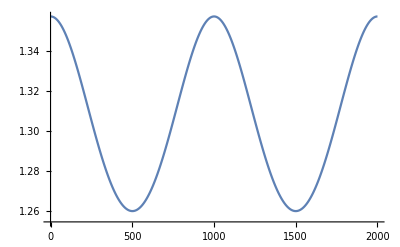

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.